```mathematica
MUonEpath=SetDirectory["/Users/isaac/Dropbox/Research_Project/2020-12-MUonE/02-Analysis/"];
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

```mathematica
e=0.303;
```

## Final Selected Cuts

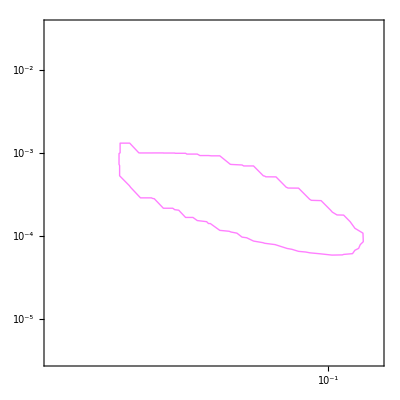

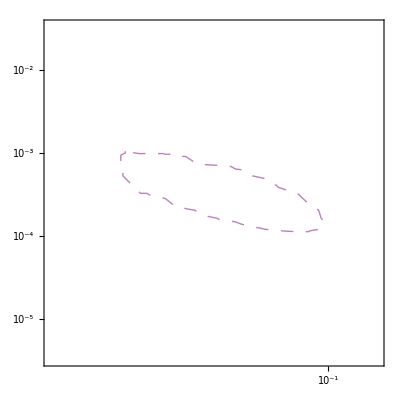

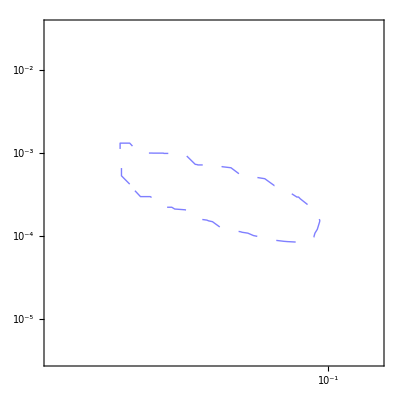

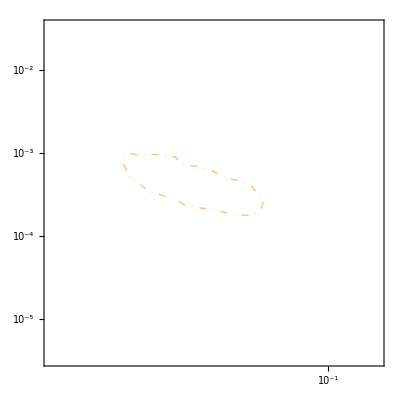

```mathematica
dataloose=Import[NotebookDirectory[]<>"output/reach_10sigma_loose.csv"][[2;;]];
loose=ListContourPlot[{Log[10,#1],Log[10,#2/e],#3} & @@@dataloose,FrameTicks->{{myTicks[-8,-2,1],None},{myTicks[-3,2,1],None}},PlotRange->{Full,Full,Full},Contours->{2.3},PlotLegends->Automatic,ContourShading->None,ImageSize->400,ContourStyle->Directive[Magenta,Thick]]
datam1=Import[NotebookDirectory[]<>"output/reach_10sigma_m1.csv"][[2;;]];
m1=ListContourPlot[{Log[10,#1],Log[10,#2/e],#3} & @@@datam1,FrameTicks->{{myTicks[-8,-2,1],None},{myTicks[-3,2,1],None}},PlotRange->{Full,Full,Full},Contours->{2.3},PlotLegends->Automatic,ContourShading->None,ImageSize->400,ContourStyle->Directive[Purple,Dashing[Medium],Thick]]
datam2=Import[NotebookDirectory[]<>"output/reach_10sigma_m2.csv"][[2;;]];
m2=ListContourPlot[{Log[10,#1],Log[10,#2/e],#3} & @@@datam2,FrameTicks->{{myTicks[-8,-2,1],None},{myTicks[-3,2,1],None}},PlotRange->{Full,Full,Full},Contours->{2.3},PlotLegends->Automatic,ContourShading->None,ImageSize->400,ContourStyle->Directive[Blue,Dashing[Large],Thick]]
datatight=Import[NotebookDirectory[]<>"output/reach_10sigma_tight.csv"][[2;;]];
tight=ListContourPlot[{Log[10,#1],Log[10,#2/e],#3} & @@@datatight,FrameTicks->{{myTicks[-8,-2,1],None},{myTicks[-3,2,1],None}},PlotRange->{Full,Full,Full},Contours->{2.3},PlotLegends->Automatic,ContourShading->None,ImageSize->400,ContourStyle->Directive[Orange,DotDashed,Thick]]
```

## Existing searches

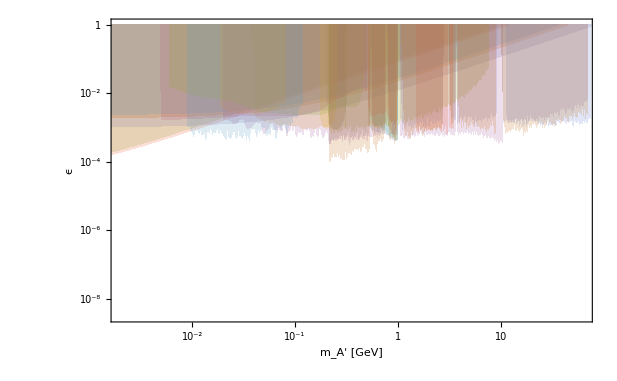

```mathematica
A12011={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/A1_Merkel2011ze.lmt","Table"],1];
A12014={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/A1_Merkel2014avp.lmt","Table"],1];
AMMe2021cs={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/AMMe_Bodas2021fsy_cs.lmt","Table"],1];
AMMe2021rb={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/AMMe_Bodas2021fsy_rb.lmt","Table"],1];
AMMmu20212l={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/AMMmu_Bodas2021fsy_2l.lmt","Table"],1];
AMMmu20212u={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/AMMmu_Bodas2021fsy_2u.lmt","Table"],1];
AMMmu2021={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/AMMmu_Bodas2021fsy.lmt","Table"],1];
APEX={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/APEX_Abrahamyan2011gv.lmt","Table"],1];
BaBar2014={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/BaBar_Lees2014xha.lmt","Table"],1];
BaBar2016={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/BaBar_TheBABAR2016rlg.lmt","Table"],1];
BESIII={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/BESIII_Ablikim2017aab.lmt","Table"],1];
CMS={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/CMS_CMS2019kiy.lmt","Table"],1];
HPS={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/HPS_Adrian2018scb.lmt","Table"],1];
KLOE2015={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Anastasi2015qla.lmt","Table"],1];
KLOE2016={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Anastasi2016ktq.lmt","Table"],1];
KLOE2018combine={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Anastasi2018azp_combined.lmt","Table"],1];
KLOE2018mu={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Anastasi2018azp_mumu.lmt","Table"],1];
KLOE2012={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Babusci2012cr.lmt","Table"],1];
KLOE2014={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/KLOE_Babusci2014sta.lmt","Table"],1];
LHCb2017prompt={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2017rft_prompt.lmt","Table"],1];
LHCb2019prompt={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2019bvg_prompt.lmt","Table"],1];
NA48={Log[10,#[[1]]],Log[10,#[[2]]]} & /@Drop[Import[MUonEpath<>"/reach/dark_photon/NA48_Batley2015lha.lmt","Table"],1];
(*recast1=ListLinePlot[{A12014,AMM,APEX,BaBar2014,KLOE1,KLOE2,KLOE3,KLOE4,LHCb,NA48},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->Top,PlotStyle->{{Yellow,Opacity[0.2]},{Gray,Opacity[0.2]},{Yellow,Opacity[0.2]},{Green,Opacity[0.2]},{Green,Opacity[0.2]},{Green,Opacity[0.2]},{Green,Opacity[0.2]},{Green,Opacity[0.2]},{Blue,Opacity[0.2]},{Magenta,Opacity[0.2]}},Axes->None,FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["g_X",14]}]/._Line:>Sequence[]*)
recast1=ListLinePlot[{A12011,A12014,AMMe2021cs,AMMe2021rb,AMMmu20212l,AMMmu20212u,AMMmu2021,APEX,BaBar2014,BaBar2016,BESIII,CMS,HPS,KLOE2015,KLOE2016,KLOE2018combine,KLOE2018mu,KLOE2012,KLOE2014,LHCb2017prompt,LHCb2019prompt,NA48},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->Top,Axes->None,FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["m_A' [GeV]",FontFamily->"Times",20],Style["ϵ",FontFamily->"Times",20]},BaseStyle->{FontFamily->"Times",20},Background->White]/._Line:>Sequence[]
```

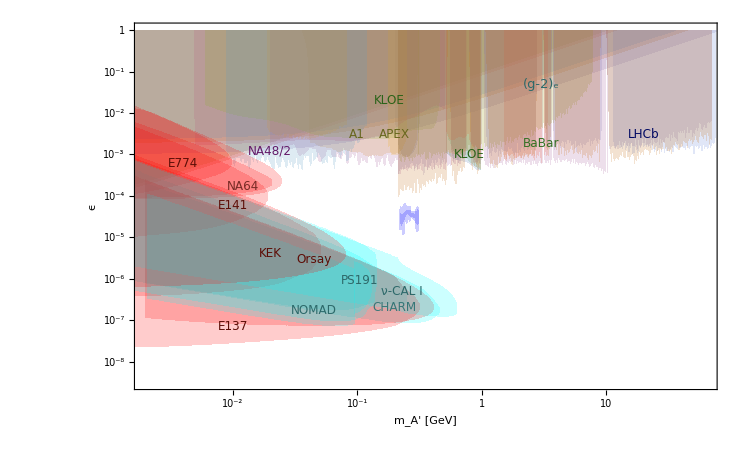

```mathematica
CHARM1985lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/CHARM_Bergsma1985qz.lmt","Table"],1],-2];
CHARM1985upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/CHARM_Bergsma1985qz.lmt","Table"],1];
CHARM1985=ListLinePlot[{CHARM1985lower,CHARM1985upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
CHARM2019lower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/CHARM_Tsai2019mtm.lmt","Table"],1];
CHARM2019upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/CHARM_Tsai2019mtm.lmt","Table"],1];
CHARM2019=ListLinePlot[{CHARM2019lower,CHARM2019upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];E1372012lower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E137_Andreas2012mt.lmt","Table"],1];
E1372012upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E137_Andreas2012mt.lmt","Table"],1];
E1372012=ListLinePlot[{E1372012lower,E1372012upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
E1372009lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E137_Bjorken2009mm.lmt","Table"],1],-2];
E1372009upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E137_Bjorken2009mm.lmt","Table"],1];
E1372009=ListLinePlot[{E1372009lower,E1372009upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
E141lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E141_Riordan1987aw.lmt","Table"],1],-2];
E141upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E141_Riordan1987aw.lmt","Table"],1];
E141=ListLinePlot[{E141lower,E141upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
E774lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E774_Bross1989mp.lmt","Table"],1],-1];
E774upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/E774_Bross1989mp.lmt","Table"],1];
E774=ListLinePlot[{E774lower,E774upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
LHCb2017lower=DeleteCases[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2017rft_displaced.lmt","Table"],1],x_/;x[[2]]≥5.];
LHCb2017upper=DeleteCases[{Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2017rft_displaced.lmt","Table"],1],x_/;x[[2]]≥5.];
LHCb2017=ListLinePlot[{LHCb2017lower,LHCb2017upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Blue,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
LHCb2019lower=DeleteCases[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2019bvg_displaced.lmt","Table"],1],x_/;x[[2]]≥5.];
LHCb2019upper=DeleteCases[{Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/LHCb_Aaij2019bvg_displaced.lmt","Table"],1],x_/;x[[2]]≥5.];
LHCb2019=ListLinePlot[{LHCb2019lower,LHCb2019upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Blue,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
KEKlower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/KEK_Konaka1986cb.lmt","Table"],1];
KEKupper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/KEK_Konaka1986cb.lmt","Table"],1];
KEK=ListLinePlot[{KEKlower,KEKupper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
NA642018lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NA64_Banerjee2018vgk.lmt","Table"],1],-5];
NA642018upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NA64_Banerjee2018vgk.lmt","Table"],1];
NA642018=ListLinePlot[{NA642018lower,NA642018upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
NA642019lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NA64_Banerjee2019hmi.lmt","Table"],1],-1];
NA642019upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NA64_Banerjee2019hmi.lmt","Table"],1];
NA642019=ListLinePlot[{NA642019lower,NA642019upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
NOMADlower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NOMAD_Astier2001ck.lmt","Table"],1];
NOMADupper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NOMAD_Astier2001ck.lmt","Table"],1];
NOMAD=ListLinePlot[{NOMADlower,NOMADupper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["g_X",14]}]/._Line:>Sequence[];
NuCAL1990lower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Blumlein1990ay.lmt","Table"],1];
NuCAL1990upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Blumlein1990ay.lmt","Table"],1];
NuCAL1990=ListLinePlot[{NuCAL1990lower,NuCAL1990upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
NuCAL1991lower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Blumlein1991xh.lmt","Table"],1];
NuCAL1991upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Blumlein1991xh.lmt","Table"],1];
NuCAL1991=ListLinePlot[{NuCAL1991lower,NuCAL1991upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
NuCAL2019lower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Tsai2019mtm.lmt","Table"],1];
NuCAL2019upper=Drop[{Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/NuCAL_Tsai2019mtm.lmt","Table"],1],-2];
NuCAL2019=ListLinePlot[{NuCAL2019lower,NuCAL2019upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
Orsaylower={Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/Orsay_Davier1989wz.lmt","Table"],1];
Orsayupper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/Orsay_Davier1989wz.lmt","Table"],1];
Orsay=ListLinePlot[{Orsaylower,Orsayupper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Red,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
PS191lower=Drop[{Log[10,#[[1]]],Log[10,#[[2]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/PS191_Bernardi1985ny.lmt","Table"],1],-2];
PS191upper={Log[10,#[[1]]],Log[10,#[[3]]]}&/@Drop[Import[MUonEpath<>"/reach/dark_photon/PS191_Bernardi1985ny.lmt","Table"],1];
PS191=ListLinePlot[{PS191lower,PS191upper},PlotRange->{{Log10[2*10^-3],1.8},{-8.5,0}},Filling->{1->{2}},Axes->None,PlotStyle->{Cyan,Opacity[0.2]},FrameTicks->{{myTicks[-8,1,1],None},{myTicks[-2,2,1],None}},PlotRangePadding->None,FrameTicksStyle->Directive[14,Black],FrameLabel->{Style["m_X [GeV]",14],Style["ϵ",14]}]/._Line:>Sequence[];
recastall=Show[recast1,CHARM1985,CHARM2019,E1372012,E1372009,E141,E774,LHCb2017,LHCb2019,KEK,NA642018,NA642019,NOMAD,NuCAL1990,NuCAL1991,Orsay,PS191,Epilog->{Inset[Style["A1",12,RGBColor[103/255,102/255,29/255]],{Log10[0.1],Log10[0.3*10^-2]}],Inset[Style["APEX",12,RGBColor[103/255,103/255,29/255]],{Log10[2*0.1],Log10[0.3*10^-2]}],Inset[Style["BaBar",12,RGBColor[54/255,114/255,37/255]],{Log10[3],Log10[18*10^-4]}],Inset[Style["CHARM",12,RGBColor[54/255,119/255,120/255]],{Log10[0.2],Log10[2*10^-7]}],Inset[Style["E137",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01],Log10[7*10^-8]}],Inset[Style["E141",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01],Log10[6*10^-5]}],Inset[Style["E774",12,RGBColor[93/255,14/255,7/255]],{Log10[0.001*4],Log10[6*10^-4]}],Inset[Style["KEK",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01*2],Log10[4*10^-6]}],Inset[Style["KLOE",12,RGBColor[43/255,99/255,25/255]],{Log10[0.1*1.8],Log10[2*10^-2]}],Inset[Style["KLOE",12,RGBColor[43/255,99/255,25/255]],{Log10[0.1*8],Log10[1*10^-3]}],Inset[Style["LHCb",12,RGBColor[0/255,8/255,98/255]],{Log10[20],Log10[3*10^-3]}],Inset[Style["NA48/2",12,RGBColor[99/255,25/255,104/255]],{Log10[0.02],Log10[1.2*10^-3]}],Inset[Style["NA64",12,RGBColor[120/255,43/255,37/255]],{Log10[0.012],Log10[1.7*10^-4]}],Inset[Style["NOMAD",12,RGBColor[45/255,105/255,106/255]],{Log10[0.045],Log10[1.7*10^-7]}],Inset[Style["ν-CAL I",12,RGBColor[45/255,105/255,106/255]],{Log10[0.23],Log10[5*10^-7]}],Inset[Style["Orsay",12,RGBColor[93/255,14/255,7/255]],{Log10[0.045],Log10[3*10^-6]}],Inset[Style["PS191",12,RGBColor[45/255,105/255,106/255]],{Log10[0.105],Log10[0.9*10^-6]}],Inset[Style["(g-2)_e",13,RGBColor[45/255,105/255,106/255]],{Log10[3],Log10[5*10^-2]}]}]
```

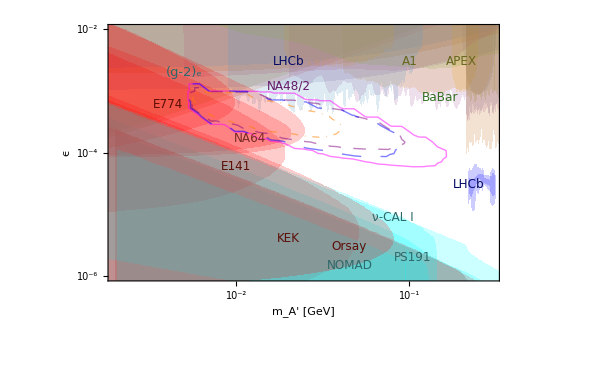

```mathematica
Show[recastall,loose,m1,m2,tight,PlotRange->{{Log10[2*10^-3],Log10[0.3]},{-6,-2}},Epilog->{Inset[Style["A1",12,RGBColor[103/255,102/255,29/255]],{Log10[0.1],Log10[0.3*10^-2]}],Inset[Style["APEX",12,RGBColor[103/255,103/255,29/255]],{Log10[2*0.1],Log10[0.3*10^-2]}],Inset[Style["BaBar",12,RGBColor[54/255,114/255,37/255]],{Log10[.15],Log10[8*10^-4]}],Inset[Style["CHARM",12,RGBColor[54/255,119/255,120/255]],{Log10[0.2],Log10[7*10^-8]}],Inset[Style["E137",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01],Log10[7*10^-8]}],Inset[Style["E141",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01],Log10[6*10^-5]}],Inset[Style["E774",12,RGBColor[93/255,14/255,7/255]],{Log10[0.001*4],Log10[6*10^-4]}],Inset[Style["KEK",12,RGBColor[93/255,14/255,7/255]],{Log10[0.01*2],Log10[4*10^-6]}],Inset[Style["KLOE",12,RGBColor[43/255,99/255,25/255]],{Log10[0.1*1.8],Log10[2*10^-2]}],Inset[Style["KLOE",12,RGBColor[43/255,99/255,25/255]],{Log10[0.1*8],Log10[1*10^-3]}],Inset[Style["LHCb",12,RGBColor[0/255,8/255,98/255]],{Log10[2*10^-2],Log10[3*10^-3]}],Inset[Style["LHCb",12,RGBColor[0/255,8/255,98/255]],{Log10[0.22],Log10[3*10^-5]}],Inset[Style["NA48/2",12,RGBColor[99/255,25/255,104/255]],{Log10[0.02],Log10[1.2*10^-3]}],Inset[Style["NA64",12,RGBColor[120/255,43/255,37/255]],{Log10[0.012],Log10[1.7*10^-4]}],Inset[Style["NOMAD",12,RGBColor[45/255,105/255,106/255]],{Log10[0.045],Log10[1.5*10^-6]}],Inset[Style["ν-CAL I",12,RGBColor[45/255,105/255,106/255]],{Log10[0.08],Log10[.9*10^-5]}],Inset[Style["Orsay",12,RGBColor[93/255,14/255,7/255]],{Log10[0.045],Log10[3*10^-6]}],Inset[Style["PS191",12,RGBColor[45/255,105/255,106/255]],{Log10[0.105],Log10[2*10^-6]}],Inset[Style["(g-2)_e",13,RGBColor[45/255,105/255,106/255]],{Log10[5*10^-3],Log10[2*10^-3]}],Inset[Framed[Column[{LineLegend[{Directive[Magenta,Thick],Directive[Purple,Dashing[Medium],Thick],Directive[Blue,Dashing[Large],Thick],Directive[Orange,DotDashed,Thick]},{Style["loose",FontFamily->"Times",FontSize->16],Style["medium-1",FontFamily->"Times",FontSize->16],Style["medium-2",FontFamily->"Times",FontSize->16],Style["tight",FontFamily->"Times",FontSize->16]}]}],RoundingRadius->5,Background->White],Scaled[{0.14,0.24}]]},ImageSize->600]
```